## Notebook to Aid in Mossbauer Data Processing for Experiment 28

## Instructions: Use this notebook to enter Mossbauer Data

```mathematica
Needs["CurveFit`"];
```

CurveFit for Mathematica v7.x thru v9.x, Version 1.91a, 1/2016

Caltech Sophomore Physics Labs, Pasadena, CA

Initialization Section... This section executes when you use the notebook.

```mathematica
Off[General::"spell1"];
```

## The Global Data

### MossData : The Processed Mosbauer Data Array,an array of data triples: {velocity(mm/sec), rate(1/sec), sigma(1/sec), counts, time (sec)}. (this array will be maintained by the fwd[],bkwd[], and zero[] functions)

```mathematica
MossData = {}
```

{}

```mathematica
LastData={}   (* The last entry made in MossData *)
```

{}

### dist : The distance the absorber travels (mm). Change this value using SetDist[ ]:

```mathematica
dist=Abs[
31.5       (* First limit of travel (mm) *)
-
8.0       (* Other limit of travel (mm) *)
]
```

23.5

## The Data Entry Functions

### This function is called by fwd[] and bkwd[] to maintain CurveFit's data arrays

```mathematica
ToCurvefitData[values_]:=
Module[{i},
(* n, xx, yy, sy, sx are Curvefit variables *)
n=Length[values];xx={};yy={};sy={};sx={};
For[i=1,i≤n,i++,
xx=Append[xx,values[[i,1]]];
yy=Append[yy,values[[i,2]]];
sy=Append[sy,values[[i,3]]];
sx=Append[sx,0];
]
]
```

### fwd[] : Call this function to add a data value for the forward (plus) direction of the absorber:

```mathematica
fwd[counts_ , time_ (* Total counts, Time (sec) *)]:=
Module[
{datum=
{dist/Abs[time],Abs[counts/time],Abs[Sqrt[Abs[counts]]/time], Abs[counts], Abs[time]}
},
LastData=datum;
MossData=Union[MossData,{datum}];
ToCurvefitData[MossData];
alldata
]
```

### bkwd[] : Call this function to add a data value for the backward (minus) direction of the absorber:

```mathematica
bkwd[counts_ , time_ (* Total counts, Time (sec) *)]:=
Module[
{datum=
{- dist/Abs[time],Abs[counts/time],Abs[Sqrt[Abs[counts]]/time], Abs[counts], Abs[time]}
},
LastData=datum;
MossData=Union[MossData,{datum}];
ToCurvefitData[MossData];
alldata
]
```

### zero[] : Call this function to add a data value for a zero-velocity data point:

```mathematica
zero[counts_ , time_ (* Total counts, Time (sec) *)]:=
Module[
{datum=
{0.0,Abs[counts/time],Abs[Sqrt[Abs[counts]]/time], Abs[counts], Abs[time]}
},
LastData=datum;
MossData=Union[MossData,{datum}];
ToCurvefitData[MossData];
alldata
]
```

### SetDist[] : Call this function to change the distance value and correctly update MossData and CurveFit:

```mathematica
SetDist[d_]:=
If[d>0,
Module[{i},
For[i=1,i≤Length[MossData],i++,
MossData[[i]]*={1.0 d/dist,1,1,1,1};
];
ToCurvefitData[MossData];
If[Length[LastData]>0,LastData *={1.0 d/dist,1,1,1,1}];
dist =d],
Print["Set the distance to a positive value!"],
Print["Set the distance to a positive value!"]
]
```

## MossData Data Manipulation/Editing Functions

### alldata : Return MossData in TableForm format, with headings

```mathematica
alldata:= TableForm[
Join[{
{"V (mm/sec)","Rate (1/sec)","sigma (1/sec)","Counts","Time (sec)"},
{"----------","------------","-------------","------","----------"}
},MossData]
]
```

### entry[] : Find a data entry with the given counts and time

```mathematica
entry[counts_ , time_ (* Total counts, Time (sec) *)]:=Module[{data=Select[MossData,(#1[[4]]==Abs[counts] && #1[[5]]==Abs[time]&),1]},
If[Length[data]>0,data[[1]],{}]
]
```

### rmdata[element] : Remove the provided element from MossData

```mathematica
rmdata[element_ (* element to be removed *)]:=
Module[{},
MossData=Complement[MossData, {element}];
ToCurvefitData[MossData];
alldata
]
```

Summary of the defined variables and functions:

MossData : 
global list variable; maintained by the functions fwd[], bkwd[], zero[], and SetDist[].
The elements of MossData are lists of the form:
{speed (mm/sec), rate (counts/sec), sigma (counts/sec), counts, time (sec)}

SetDist[distance (mm)] :
function; sets or changes the distance the absorber travels. Updates both MossData and the CurveFit data sets.

fwd[counts, time (sec)] :
function; adds a data point for travel in the forward (+) direction. Updates both MossData and the CurveFit data sets.

bkwd[counts, time (sec)] :
function; adds a data point for travel in the backward (-) direction. Updates both MossData and the CurveFit data sets.

zero[counts, time (sec)] :
function; adds a zero-velocity data point. Updates both MossData and the CurveFit data sets.

LastData : 
global variable; contains the last data element inserted into MossData by one of the functions fwd[], bkwd[], and zero[]. LastData is a list of the form:
{speed (mm/sec), rate (counts/sec), sigma (counts/sec), counts, time (sec)}

alldata : 
this "function" takes no arguments; executing alldata returns the contents of MossData as a table with headings.

entry[counts, time (sec)] :
function; finds an entry (element) in MossData with the specified counts and time, if it exists. The returned value is a list of the form (a null list is returned if no entry could be found):
{speed (mm/sec), rate (counts/sec), sigma (counts/sec), counts, time (sec)}

rmdata[entry] :
function; removes the specified entry (element) from MossData and the CurveFit data sets. the specified entry should be a list as returned by entry[] or LastData.

Here Are a Couple of Calls to the data entry functions. You should replace these lines with your own commands to enter the data you take.

```mathematica
(* Empty the Mossbauer data set *)
MossData = {}
```

{}

```mathematica
(* Set or change the distance the absorber travels (in mm) *)
SetDist[3.20-0.75]
```

2.45

```mathematica
(* Add a forward measurement *)
fwd[38529,141.000];
```

```mathematica
(* Add a backward measurement *)
bkwd[36976,140.696];
```

```mathematica
(* Display the data so far *)
alldata
```

V (mm/sec) | Rate (1/sec) | sigma (1/sec) | Counts | Time (sec)
---------- | ------------ | ------------- | ------ | ----------

```mathematica
(* Here's the last data entry made *)
LastData
```

```mathematica
(* Here's how to remove data points, in case you make a mistake *)
rmdata[LastData];
(* or *)
rmdata[entry[38529,141]];
```

```mathematica
(* Now there should be no remaining data *)
alldata
```

You can enter your own data and commands following this line.

```mathematica
(* Your commands *)
```

```mathematica
SetDist[32.0-7.5]
```

24.5

```mathematica
fwd[21932,110.54]
```

V (mm/sec) | Rate (1/sec) | sigma (1/sec) | Counts | Time (sec)
---------- | ------------ | ------------- | ------ | ----------
0.221639 | 198.408 | 1.33974 | 21932 | 110.54

```mathematica
bkwd[19143,120.65]
```

V (mm/sec) | Rate (1/sec) | sigma (1/sec) | Counts | Time (sec)
---------- | ------------ | ------------- | ------ | ----------
-0.203067 | 158.666 | 1.14677 | 19143 | 120.65
0.221639 | 198.408 | 1.33974 | 21932 | 110.54

```mathematica
zero[12839,72.95]
```

V (mm/sec) | Rate (1/sec) | sigma (1/sec) | Counts | Time (sec)
---------- | ------------ | ------------- | ------ | ----------
-0.203067 | 158.666 | 1.14677 | 19143 | 120.65
0. | 175.997 | 1.55325 | 12839 | 72.95
0.221639 | 198.408 | 1.33974 | 21932 | 110.54

```mathematica
fwd[10396,51.85];
```

```mathematica
bkwd[9858,54.38];
```

```mathematica
fwd[7207,35.60];
```

```mathematica
bkwd[7332,36.86];
```

```mathematica
fwd[6181,30.26];
```

```mathematica
bkwd[6424,30.96];
```

```mathematica
fwd[7271,35.47];
```

```mathematica
bkwd[7409,36.87];
```

```mathematica
fwd[8557,42.24];
```

```mathematica
bkwd[8371,43.78];
```

```mathematica
fwd[9471,46.38];
```

```mathematica
bkwd[9090,48.38];
```

```mathematica
fwd[10050,49.09];
```

```mathematica
bkwd[9585,51.51];
```

```mathematica
fwd[10239,50.45];
```

```mathematica
bkwd[9693,52.85];
```

```mathematica
zero[12443,70.03];
```

```mathematica
fwd[10583,52.21];
```

```mathematica
bkwd[10098,54.59];
```

```mathematica
fwd[9403,46.58];
```

```mathematica
bkwd[9190,48.40];
```

```mathematica
fwd[12208,59.83];
```

```mathematica
bkwd[10649,62.61];
```

```mathematica
fwd[12480,62.34];
```

```mathematica
bkwd[11153,64.81];
```

```mathematica
fwd[13584,67.92];
```

```mathematica
bkwd[11721,70.49];
```

```mathematica
fwd[16326,81.85];
```

```mathematica
bkwd[13551,85.26];
```

```mathematica
fwd[17015,86.44];
```

```mathematica
bkwd[14487,90.55];
```

```mathematica
fwd[21371,108.31];
```

```mathematica
bkwd[18492,118.03];
```

```mathematica
fwd[27553,141.62];
```

```mathematica
bkwd[24105,152.74];
```

```mathematica
zero[10903,61.59];
```

```mathematica
fwd[60093,323.10];
```

```mathematica
bkwd[61704,370.35];
```

```mathematica
fwd[26483,136.39];
```

```mathematica
bkwd[23364,148.18];
```

```mathematica
fwd[40681,214.87];
```

```mathematica
bkwd[38081,236.38]
```

V (mm/sec) | Rate (1/sec) | sigma (1/sec) | Counts | Time (sec)
---------- | ------------ | ------------- | ------ | ----------
-0.791344 | 207.494 | 2.58882 | 6424 | 30.96
-0.664677 | 198.915 | 2.32304 | 7332 | 36.86
-0.664497 | 200.949 | 2.33457 | 7409 | 36.87
-0.559616 | 191.206 | 2.08984 | 8371 | 43.78
-0.506408 | 187.888 | 1.97068 | 9090 | 48.38
-0.506198 | 189.876 | 1.98067 | 9190 | 48.4
-0.475636 | 186.08 | 1.90066 | 9585 | 51.51
-0.463576 | 183.406 | 1.86288 | 9693 | 52.85
-0.450533 | 181.28 | 1.82581 | 9858 | 54.38
-0.4488 | 184.979 | 1.84079 | 10098 | 54.59
-0.391311 | 170.085 | 1.6482 | 10649 | 62.61
-0.378028 | 172.088 | 1.6295 | 11153 | 64.81
-0.347567 | 166.279 | 1.53587 | 11721 | 70.49
-0.287356 | 158.937 | 1.36534 | 13551 | 85.26
-0.270569 | 159.989 | 1.32923 | 14487 | 90.55
-0.207574 | 156.672 | 1.15212 | 18492 | 118.03
-0.203067 | 158.666 | 1.14677 | 19143 | 120.65
-0.165339 | 157.673 | 1.03154 | 23364 | 148.18
-0.160403 | 157.817 | 1.01648 | 24105 | 152.74
-0.103647 | 161.101 | 0.82555 | 38081 | 236.38
-0.0661536 | 166.61 | 0.670725 | 61704 | 370.35
0. | 175.997 | 1.55325 | 12839 | 72.95
0. | 177.025 | 1.69536 | 10903 | 61.59
0. | 177.681 | 1.59286 | 12443 | 70.03
0.0758279 | 185.989 | 0.758709 | 60093 | 323.1
0.114022 | 189.328 | 0.938685 | 40681 | 214.87
0.172998 | 194.556 | 1.17209 | 27553 | 141.62
0.179632 | 194.171 | 1.19317 | 26483 | 136.39
0.221639 | 198.408 | 1.33974 | 21932 | 110.54
0.226203 | 197.313 | 1.34972 | 21371 | 108.31
0.283434 | 196.842 | 1.50904 | 17015 | 86.44
0.299328 | 199.462 | 1.56107 | 16326 | 81.85
0.360718 | 200. | 1.716 | 13584 | 67.92
0.393006 | 200.192 | 1.79201 | 12480 | 62.34
0.409494 | 204.045 | 1.84673 | 12208 | 59.83
0.469259 | 202.701 | 1.97038 | 10583 | 52.21
0.472517 | 200.501 | 1.96646 | 10396 | 51.85
0.485629 | 202.953 | 2.00571 | 10239 | 50.45
0.499083 | 204.726 | 2.04216 | 10050 | 49.09
0.525977 | 201.868 | 2.08177 | 9403 | 46.58
0.528245 | 204.204 | 2.0983 | 9471 | 46.38
0.580019 | 202.58 | 2.18996 | 8557 | 42.24
0.688202 | 202.444 | 2.38466 | 7207 | 35.6
0.690725 | 204.99 | 2.40401 | 7271 | 35.47
0.80965 | 204.263 | 2.59813 | 6181 | 30.26

```mathematica
fwd[13577,68.21];
```

```mathematica
bkwd[6209,31.23];
```

```mathematica
fwd[5018,24.53];
```

```mathematica
bkwd[4542,22.65];
```

```mathematica
LorentzianCFit[]
```

n = 49

y(ω) = c ± y_max
(γ/2)^2/(ω - ω_0)^2 +
(γ/2)^2

Fit of (x,y)  (unweighted)

y_max= 
-53.2616 | c= 
208.565 | 
σ_y_max= 
1.04333 | σ_c= 
0.768154 | 
ω_0= 
-0.205745 | γ= 
0.483496 | 
σ_ω_0= 
0.00425524 | σ_γ= 
0.0179983 | Std. deviation= 
2.18225

Fit of (x,y±σ_y)

y_max= 
-54.272 | c= 
209.868 | 
σ_y_max= 
0.740065 | σ_c= 
0.708058 | 
ω_0= 
-0.203336 | γ= 
0.507115 | 
σ_ω_0= 
0.00259516 | σ_γ= 
0.012653 | χ^2/(n-4)= 
1.58274

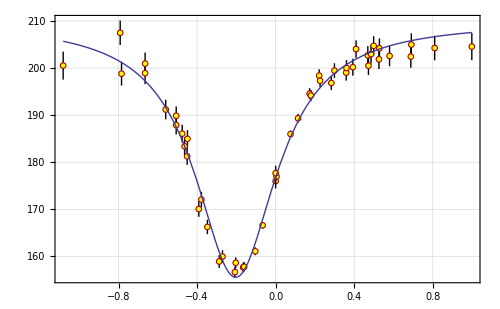
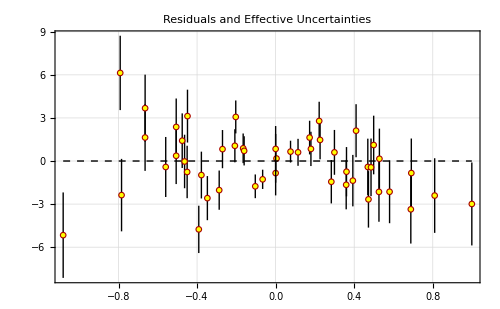
-Graphics-
-Graphics-
y(ω) = c ± y_max
(γ/2)^2/(ω - ω_0)^2 +
(γ/2)^2
y_max= 
-54.272 | c= 
209.868 | 
σ_y_max= 
0.740065 | σ_c= 
0.708058 | 
ω_0= 
-0.203336 | γ= 
0.507115 | 
σ_ω_0= 
0.00259516 | σ_γ= 
0.012653 | χ^2/(n-4)= 
1.58274

```mathematica
LinearDifferencePlot[]
```

```mathematica
xnew[ x_, y_ ] := x 
ynew[ x_, y_ ] := -y 
DataTransform[]
(* Use Undo[] if you don't like the results. *)
```

All 49 points transformed.

```mathematica
GaussianCFit[]
```

n = 49

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
45.6336 | c= 
-202.573 | 
σ_y_max= 
0.778016 | σ_c= 
0.447509 | 
μ= 
-0.203889 | sigma= 
0.198531 | 
σ_μ= 
0.00347863 | σ_sigma= 
0.00453425 | Std. deviation= 
1.8679

Fit of (x,y±σ_y)

y_max= 
45.3838 | c= 
-202.164 | 
σ_y_max= 
0.576699 | σ_c= 
0.481576 | 
μ= 
-0.203715 | sigma= 
0.197246 | 
σ_μ= 
0.00253836 | σ_sigma= 
0.00357065 | χ^2/(n-4)= 
1.00852

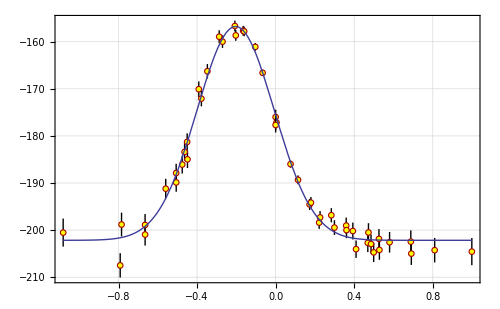
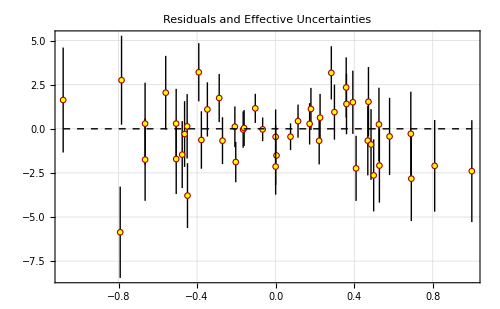
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c
y_max= 
45.3838 | c= 
-202.164 | 
σ_y_max= 
0.576699 | σ_c= 
0.481576 | 
μ= 
-0.203715 | sigma= 
0.197246 | 
σ_μ= 
0.00253836 | σ_sigma= 
0.00357065 | χ^2/(n-4)= 
1.00852

```mathematica
LinearDifferencePlot[]
```

```mathematica
zero[19071,107.94];
```

```mathematica
bkwd[4239,20.65];
```

```mathematica
With[  {name = SystemDialogInput["FileSave", DataFileName]},
  If[ name =!= $Canceled, SaveFile[name]]
]
```

```mathematica
With[  {name = SystemDialogInput["FileSave", DataFileName]},
  If[ name =!= $Canceled, SaveFile[name]]
]
```

Sorted data saved in C:\Users\student\Documents\Mossbauer_BadalYovan_2_20_2018